```mathematica
SetDirectory[NotebookDirectory[]];
Import["Modules/Welcome.m"];
Import["Modules/File_manager.m"];
Import["Modules/SlideMenuManager.m"];
ModuleDirectoryMenu["_intro"];
(*ModuleWelcome [];
Init[NotebookDirectory[]];
UserList = AddUser["Pitagora"];
Echo[UserList[[1]]];
UserList[[2]] = 3;
SaveUserData[UserList];*)
```

Introduzione | Esempi | Esercizi | Teoria

## Home

This is a text cell.

```mathematica
SetDirectory[NotebookDirectory[]];
Import["Modules/User.m"];
Import["Modules/File_manager.m"];
Import["Modules/User_login.m"];
Init[ NotebookDirectory[] ];
GetUserLoginGraphicInterface[];
```

Registrazione

Inserisci il tuo nome nel campo seguente per salvare i tuoi progressi

Inserisci il tuo nome

Benvenuto/a davide

Ecco i tuoi progressi

Eculide Es.1 | Euclide es.2 | Pitagora es.1 | Pitagora es.2 | Pitagora es.3 | Pitagora es.4
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## User

```mathematica
CellPrint[TextCell["","",CellTags->{"_intro"}]];
```

## Bibliografia

This is a text cell.

## Prereqs

This is a text cell.

## Note

This is a text cell.

## Euclide: Enunciato

Teorema di Euclide

In un triangolo rettangolo il quadrato costruito un cateto è equivalente al rettangolo che ha i lati congruenti all'ipotenusa e alla proiezione dello stesso cateto su di essa.

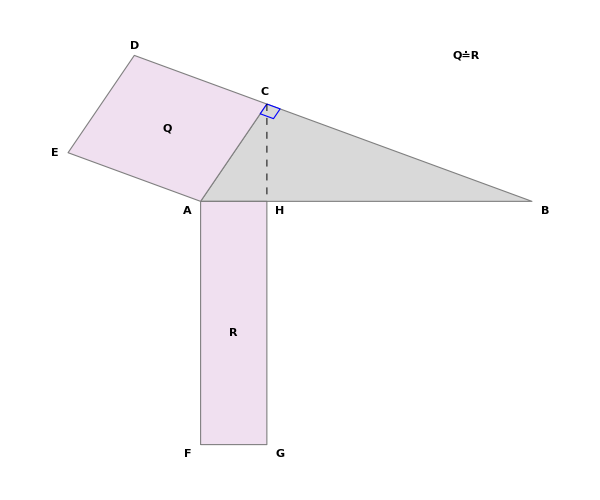

```mathematica
SetDirectory[NotebookDirectory[]];
Import["Modules/EuclideEnunciato.m"];
ModuleEuclideEnunciato[];
```

This is a text cell.

## Euclide: Dimostrazione

```mathematica
SetDirectory[NotebookDirectory[]];
Import["Modules/EuclideDimostrazione.m"];
ModuleEuclideDimostrazione [];
```

Dimostrazione del teorema di Euclide

## Euclide: Esempi

Teorema di Euclide - Spiegazione matematica

-Graphics-

Seguendo l'enunciato del primo teorema di Euclide avremo che

AC^2 = AH x AB

AC^2 rappresenta l'area del quadrato costruito sul cateto AC, mentre AH x AB è l'area del rettangolo che ha per dimensioni la proiezione
del cateto AC sull'ipotenusa e l'ipotenusa stessa

Alla luce di questo possiamo affermare che: in un triangolo rettangolo, ciascun cateto è il medio proporzionaletra l'ipotenusa e la proiezione
del cateto sull'ipotenusa

In formule questo si traduce nelle seguenti proporzioni:

AB : CB = CB : HB

AB : AC = AC : AH

Esempio esercizio

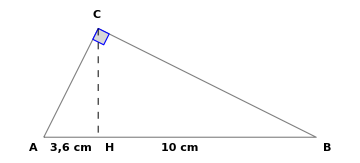

Calcolare il perimetro del triangolo rettangolo la cui ipotenusa misura 10 cm e la proiezione del cateto minore sull'ipotenusa misura 3,6 cm

Risoluzione

Conosciamo l'ipotenusa AB = 10 cm e la proiezione del cateto minore sull'ipotenusa AH = 3.6 cm. Grazie al primo teorema di Euclide 
possiamo costruire la proporzione per calcolare la lunghezza del cateto minore AC :

AB : AC = AC : AH

Sostituendo i dati avremo:

10 : AC = AC : 3,6

Utilizzando la proprietà fondamentale delle proporzioni otteniamo:

AC^2 =  10 x 3,6

AC = √36 = 6 cm

Possiamo ricavare adesso BH come differenza (AB - AH) :

BH =  10 - 3,6 = 6,4 cm

Utilizziamo infine il teorema di Euclide per determinare la lunghezza del cateto maggiore BC :

AB : BC = BC : BH

10 : BC = BC : 6,4

BC^2 =  10 x 6,4

BC = √64 = 8 cm

Infine il perimetro P è dato dalla somma della lunghezza dei lati ottenuti:

P = AB + BC + AC = 10 + 8 + 6 = 24 cm

```mathematica
SetDirectory[NotebookDirectory[]];
Import["Modules/EuclideEsempi.m"];
ModuleEuclideEsempi [];
```

This is a text cell.

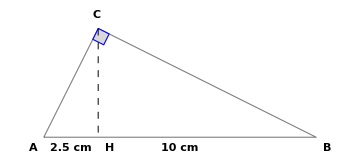

Calcolare la lunghezza del lato AC del triangolo rettangolo la cui ipotenusa misura 10 cm e la proiezione del cateto minore sull'ipotenusa misura 2.5 cm

Result: 5.

Verifica

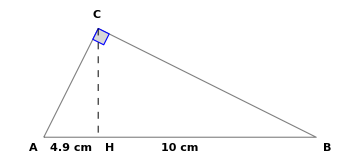

Calcolare il perimetro del triangolo rettangolo la cui ipotenusa misura 10 cm e la proiezione del cateto minore sull'ipotenusa misura 4.9 cm

Result: 24.14

Verifica

```mathematica
SetDirectory[NotebookDirectory[]];
Import["Modules/EuclideEsercizi.m"];
ModuleEuclideEsercizi [];
```

## Euclide: Esercizi

This is a text cell.

## Pitagora: Enunciato

Teorema di Pitagora

In un triangolo rettangolo il quadrato costruito sull'ipotenusa è equivalente alla somma dei quadrati costruiti sui cateti.

AB^2+BC^2=AC^2

Oppure

Q_c1+Q_c2=Q_i

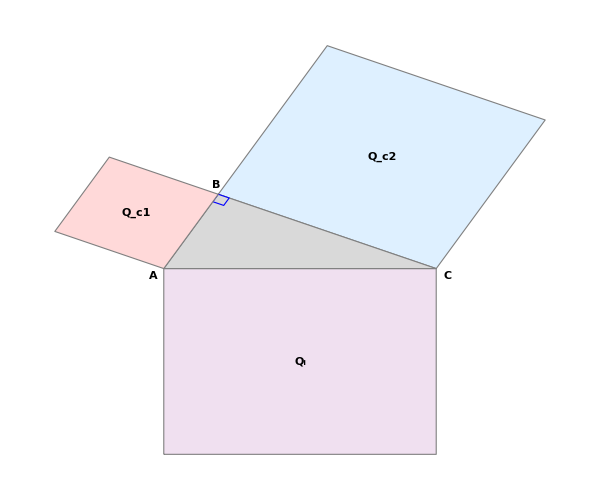

```mathematica
SetDirectory[NotebookDirectory[]];
Import["Modules/PitagoraEnunciato.m"];
ModulePitagoraEnunciato [];
```

This is a text cell.

## Pitagora: Dimostrazione

```mathematica
SetDirectory[NotebookDirectory[]];
Import["Modules/PitagoraDimostrazione.m"];
ModulePitagoraDimostrazione [];
```

Dimostrazione del teorema di Pitagora

This is a text cell.

## Pitagora: Esempi

```mathematica
SetDirectory[NotebookDirectory[]];
Import["Modules/PitagoraEsempi.m"];
ModulePitagoraEsempi [];
```

Dimostrazione Grafica:

This is a text cell.

Triad: 3

Data la triade pitagorica a,b,c determinare b sapendo che a = 3 e c = 5

Result: 4.0

Verifica

Data la triade pitagorica a,b,c determinare b sapendo che a = 9 e c = 41

Result: 40.

Verifica

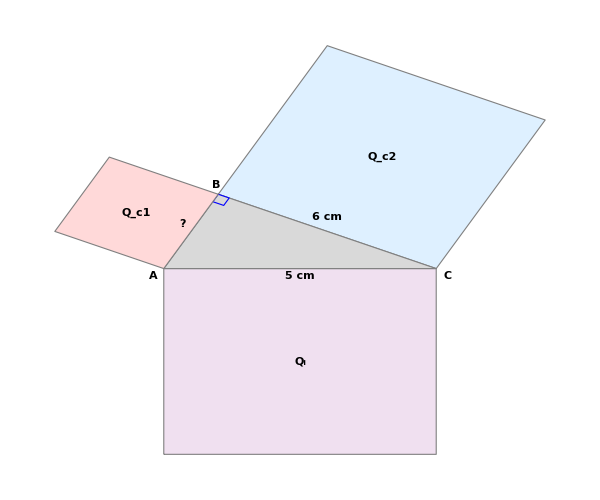

Dato il triangolo ABC, calcolare la lunghezza del cateto AB e l'area del quadrato Q_c1 sapendo che il lato AC è lungo 5cm e il lato BC è lungo 6cm

Nel caso di risultato con cifre decimali, arrotondare alla prima cifra

Result: 11.0

Verifica

Esercizi

-Graphics-

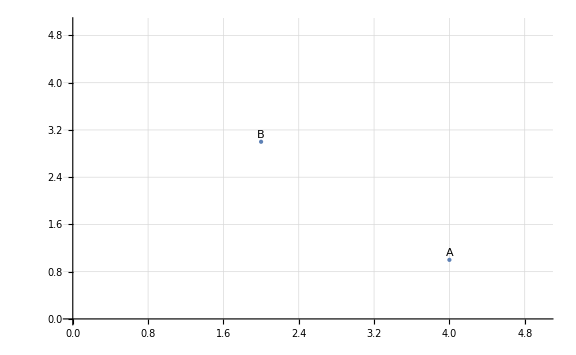

Calcola la distanza tra i due punti A e B sul piano cartesiano

Nel caso di risultato con cifre decimali, arrotondare alla prima cifra

Verifica

distance: 2.8

distance: 2.8

distance: 2.8

«1 more identical outputs»

```mathematica
SetDirectory[NotebookDirectory[]];
Import["Modules/PitagoraEsercizi.m"];
ModulePitagoraEsercizi [];
```

## Pitagora: Esercizi

This is a text cell.